# (* Test Notebook for Linear Evolution. *)

#### (* Initial findings: two approximations in the construction of δU(0) currently implemented in Python introduce an unacceptable loss of precision. *)

(* Method: Use eq. (70) to compute Bn, Cn, from \delta_U(\xi=0) [eq. (18)],  noting that t(\xi) is eq. (37).  Then construct δρ from eq. (43), δm from eq. (46). *)

#### (* 0. Model *)

```mathematica
rparam=2;
pparam = H (3/2 - Sqrt[(9/4) - μψ^2]);
λ[t_]= -(3/2)  + Sqrt[(9/4)  +μ0^2(1- Exp[-rparam pparam t])];
μψtilde= Sqrt[- rparam pparam/H];

params = {μψ-> 1/10, H->1,μ0->10,Ne->15,RH->1}
```

{μψ→1/10,H→1,μ0→10,Ne→15,RH→1}

(* Dummy initial spatial profile \Phi(r). Define rbar and r*)

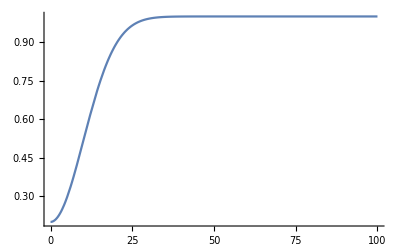

```mathematica
Plot[1- 0.8Exp[-(1/2)x^2/100],{x,0,100},PlotRange->All]
```

```mathematica
(* Phirbar[rbar_] = Exp[-rbar^2]; *)

(* Use Phi(rbar) of recent numerical experiments by Michelle: *)
Phirbar[rbar_] =1-(4/5) Exp[-rbar^2/200];

(* Relation to r: r(rbar) and rbar(r)*)
rbarfunr = r/( RH Exp[Ne]);
rfunrbar=RH Exp[Ne] rbar;
(* Phi(r) from eq. 3 of Michelle's note:*)
Phir[r_] = Phirbar[rbarfunr];
```

#### (*1. Compute Time Delay : take t0=Ne/H is the end of inflation (as defined wrt the waterfall transition)*)

```mathematica
δτ[r_] = -1/(2 λ[Ne/H] H ) Log[Phir[r]];
dδτ[r_]= D[δτ[r],r];
```

#### (* 2. Construct δU(ξ=0). Note t0= H Ne *)

```mathematica
βt = β-> 1/(2 λ[Ne/H]); 
A[r_] = r Phir[r]^(-β); 
Abar[r_]= A[r] H;
Abarmax= Abar[rmax] /.βt;
```

#### (* Note we cannot analytically solve for r(Abar): *)

```mathematica
Solve[FullSimplify[Abar[r]/.βt/.params]==Asol,r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(1-4/5 ⅇ^(-r^2/(200 ⅇ^30)))^(-1/(-3+(√(409 ⅇ^45-400 ⅇ^(12 √14)))/ⅇ^(45/2))) r==Asol,r]

```mathematica
(* So we do this by interpolation.*)
```

```mathematica
Abar[r_]= A[r] H;
rAbarTable = Table[{Abar[r]/.βt/.params,r} /. r-> i  10^7,{i,.5,7.01,.01}];
rofAInterp=Interpolation[rAbarTable];
```

```mathematica
Clear[Abar]

(* map r to Abar using interpolation:*)
rfunAbar = r-> rofAInterp[Abar] ;

(* δU in r-space:  eq 14 o June 19 note *)

 δU0r[r_] = (1 + Exp[- H δτ[r]]dδτ[r]/(H A[r]))/Sqrt[1 - (Exp[- H δτ[r]] dδτ[r])^2] - 1;  
δU0rErrorProne[r_] = (1 + Exp[- H δτ[r]]dδτ[r]/(H A[r]))/Sqrt[1 - (Exp[- H δτ[r]] dδτ[r])^2] - 1;  

(* Rewrite this in a way that Mathematica deals with better:
δU0 = (1 +C1) /C2 - 1 =C1/C2 + (1 - C2)/C2
*)
C1= Exp[- H δτ[r]]dδτ[r]/(H A[r]);
C2 = Sqrt[1 - (Exp[- H δτ[r]] dδτ[r])^2];
δU0r[r_] =C1/C2+ (1- C2)/C2;

(* Find δU on interpolated Abar space. First go from r to rbar: *)
δU0rbar[rbar_] = δU0r[rfunrbar];
(* Clear Abar to use it as a independent variable, and not a function:*)
Clear[Abar]
(* Now go to Abar space:*)
δU0Abar=δU0r[r] /.  rfunAbar;
```

#### (* As an alternative check, we can do this without interpolation r(A): *)

```mathematica
Abar[r_]= A[r] H;
δU0NoAbarInterpTable = Table[{Abar[r]/.βt/.params,δU0r[r]/.βt/.params} /. r-> i  10^8,{i,0.009,3.1,.01}];
δU0NoAbarInterpInterp=Interpolation[δU0NoAbarInterpTable];
Clear[Abar]
```

#### (* Let’s also try the Taylor expanded form, eq. (18) of the June 19th note. This is what is implemented in Python.*)

```mathematica
δU0Altr[r_] = -(1/(A[r] H))Exp[- Ne] β Phir[r]^(β-1) (D[Phirbar[rbar],rbar]/.rbar-> rbarfunr) + Exp[-2 Ne] (1/2)β^2 Phir[r]^(2β-2) (D[Phirbar[rbar],rbar]/.rbar-> rbarfunr)^2;
δU0AltAbar =δU0Altr[r] /.  rfunAbar;
```

```mathematica
N[-(1/(A[r] H))Exp[- Ne] β Phir[r]^(β-1) (D[Phirbar[rbar],rbar]/.rbar-> rbarfunr)/.βt /. params/. r->10^7]
```

-3.70614×10^-16

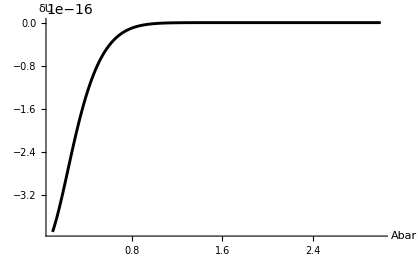

```mathematica
Plot[δU0AltAbar/.βt/.params,{Abar, 10^7,3 10^8},AxesLabel->{Style["Abar",Large,Bold],Style["δU",Large,Bold]},PlotStyle->{{Black,Thickness[.005]},{Red,Dashed}},AxesStyle->Black,PlotPoints->1000,PlotRange->All]
```

## Michelle’s Tests

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/michellexu/black-holes-stack/scratchspace

```mathematica
rlist = Import["deltaU0s.csv", {"Data",1}];
```

```mathematica
deltaUpythonlist= Import["deltaU0s.csv", {"Data",2}]
```

{-3.70989332130729193×10^-16,-3.60214200211688135×10^-16,-3.41053699232852259×10^-16,-3.17004199792037833×10^-16,-2.91227304492876767×10^-16,-2.658313790580576×10^-16,-2.41876987860423939×10^-16,-2.19701034187489722×10^-16,-1.99251310716763993×10^-16,-1.80320263035520313×10^-16,-1.62677458255546399×10^-16,-1.46131929913164945×10^-16,-1.30553396826298539×10^-16,-1.15871766648445902×10^-16,-1.02066330722127459×10^-16,-8.91510023884279593×10^-17,-7.71590972906913588×10^-17,-6.61295950842516642×10^-17,-5.6095937634667992×10^-17,-4.70778632934506415×10^-17,-3.90763830613056536×10^-17,-3.20717050157742884×10^-17,-2.60236895510392661×10^-17,-2.08742696554815988×10^-17,-1.6551199820019374×10^-17,-1.29725008921634419×10^-17,-1.00510351098494386×10^-17,-7.6987578678800856×10^-18,-5.83032917824133831×10^-18,-4.36590722415162962×10^-18,-3.23307139024540112×10^-18,-2.36792091729306986×10^-18,-1.71546253065569739×10^-18,-1.22943643814672729×10^-18,-8.71739597235604471×10^-19,-6.11595015348086746×10^-19,-4.24593490927454724×10^-19,-2.91706255904880975×10^-19,-1.98338543692233831×10^-19,-1.33468538873441077×10^-19,-8.88952357360962733×10^-20,-5.86029798000804993×10^-20,-3.82396026852921111×10^-20,-2.46983434804547539×10^-20,-1.57902628416000944×10^-20,-9.9926955352117412×10^-21,-6.25966575723043208×10^-21,-3.88147950966841781×10^-21,-2.38244492120753006×10^-21,-1.44753502278716567×10^-21,-8.70596202078556111×10^-22,-5.18306309555188386×10^-22,-3.05448946516468492×10^-22,-1.78185931150116625×10^-22,-1.02894219463301932×10^-22,-5.88154483582378858×10^-23,-3.32793439609936241×10^-23,-1.86397903484841266×10^-23,-1.03345176283322986×10^-23,-5.67181820227808678×10^-24,-3.08132334590911423×10^-24,-1.65704804132857923×10^-24,-8.82095794493898317×10^-25,-4.6481402482626621×10^-25,-2.42451804346459779×10^-25,-1.25185588529424606×10^-25,-6.39832017897661061×10^-26,-3.23712868181715106×10^-26,-1.62120155614545312×10^-26,-8.0370629327868998×10^-27,-3.94401889775024891×10^-27,-1.91584011386309598×10^-27,-9.2121783896887303×10^-28,-4.38497215881869708×10^-28,-2.06618814991730048×10^-28,-9.63610321948214951×10^-29,-4.4489358403990554×10^-29,-2.03317666724728453×10^-29,-9.17704686095654453×10^-30,-4.09853842962449807×10^-30,-1.83408003678183287×10^-30,-8.12085787388303946×10^-31,-3.39410213703322418×10^-31,-1.5242973669310992×10^-31,-9.03755006902346118×10^-32,-2.97728257634496766×10^-32,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

These are the delta_U values from Python.

```mathematica
deltaUmathlist = δU0Altr /@rlist/.βt/.params
```

{-4.21129067318936947833000052643041×10^-16,-4.2112906731893535374448775084846×10^-16,-4.21129067318932165567463147298×10^-16,-4.211290673189273833019262420741×10^-16,-4.211290673189210069478770352923×10^-16,-4.21129067318913036505315527114×10^-16,-4.211290673189034719742417177477×10^-16,-4.211290673188923133546556074161×10^-16,-4.211290673188795606465571964062×10^-16,-4.211290673188652138499464850372×10^-16,-4.21129067318849272964823473668×10^-16,-4.21129067318831737991188162698×10^-16,-4.21129067318812608929040552601×10^-16,-4.21129067318791885778380643788×10^-16,-4.21129067318769568539208436811×10^-16,-4.21129067318745657211523932228×10^-16,-4.21129067318720151795327130638×10^-16,-4.21129067318693052290618032678×10^-16,-4.2112906731866435869739663903×10^-16,-4.211290673186340710156629504×10^-16,-4.2112906731860218924541696757×10^-16,-4.2112906731856871338665869131×10^-16,-4.2112906731853364343938812248×10^-16,-4.2112906731849697940360526195×10^-16,-4.2112906731845872127931011077×10^-16,-4.2112906731841886906650266964×10^-16,-4.2112906731837742276518293967×10^-16,-4.2112906731833438237535092192×10^-16,-4.2112906731828974789700661745×10^-16,-4.2112906731824351933015002739×10^-16,-4.2112906731819569667478115289×10^-16,-4.2112906731814627993089999515×10^-16,-4.211290673180952690985065554×10^-16,-4.2112906731804266417760083493×10^-16,-4.2112906731798846516818283504×10^-16,-4.211290673179326720702525571×10^-16,-4.211290673178752848838100025×10^-16,-4.2112906731781630360885517268×10^-16,-4.2112906731775572824538806912×10^-16,-4.2112906731769355879340869332×10^-16,-4.2112906731762979525291704686×10^-16,-4.2112906731756443762391313131×10^-16,-4.2112906731749748590639694833×10^-16,-4.2112906731742894010036849958×10^-16,-4.2112906731735880020582778678×10^-16,-4.2112906731728706622277481169×10^-16,-4.211290673172137381512095761×10^-16,-4.2112906731713881599113208184×10^-16,-4.2112906731706229974254233135×10^-16,-4.2112906731698418940544032545×10^-16,-4.2112906731690448497982606663×10^-16,-4.2112906731682318646569955689×10^-16,-4.2112906731674029386306079826×10^-16,-4.2112906731665580717190979282×10^-16,-4.2112906731656972639224654269×10^-16,-4.2112906731648205152407105001×10^-16,-4.2112906731639278256738331698×10^-16,-4.2112906731630191952218334584×10^-16,-4.2112906731620946238847113886×10^-16,-4.2112906731611541116624669835×10^-16,-4.2112906731601976585551002668×10^-16,-4.2112906731592252645626112622×10^-16,-4.2112906731582369296849999943×10^-16,-4.2112906731572326539222664876×10^-16,-4.2112906731562124372744107674×10^-16,-4.2112906731551762797414328592×10^-16,-4.2112906731541241813233327889×10^-16,-4.2112906731530561420201105828×10^-16,-4.2112906731519721618317662678×10^-16,-4.2112906731508722407582998708×10^-16,-4.2112906731497563787997114196×10^-16,-4.2112906731486245759560009419×10^-16,-4.2112906731474768322271684661×10^-16,-4.2112906731463131476132140209×10^-16,-4.2112906731451335221141376355×10^-16,-4.2112906731439379557299393394×10^-16,-4.2112906731427264484606191626×10^-16,-4.2112906731414990003061771352×10^-16,-4.2112906731402556112666132882×10^-16,-4.2112906731389962813419276525×10^-16,-4.2112906731377210105321202598×10^-16,-4.2112906731364297988371911419×10^-16,-4.2112906731351226462571403311×10^-16,-4.2112906731337995527919678602×10^-16,-4.2112906731324605184416737623×10^-16,-4.211290673131105543206258071×10^-16,-4.21129067312973462708572082×10^-16,-4.2112906731283477700800620438×10^-16,-4.211290673126944972189281777×10^-16,-4.2112906731255262334133800548×10^-16,-4.2112906731240915537523569127×10^-16,-4.2112906731226409332062123865×10^-16,-4.2112906731211743717749465127×10^-16,-4.2112906731196918694585593278×10^-16,-4.2112906731181934262570508691×10^-16,-4.211290673116679042170421174×10^-16,-4.211290673115148717198670302×10^-16,-4.2112906731136024513417982485×10^-16,-4.2112906731120402445998050735×10^-16,-4.211290673110462096972690816×10^-16}

```mathematica
deltaUerror = deltaUpythonlist - deltaUmathlist;
```

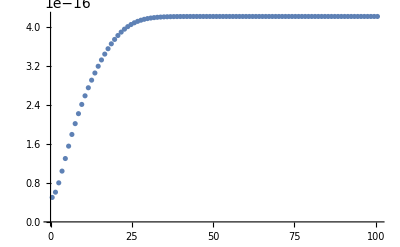

```mathematica
ListPlot[Transpose[List[rlist,deltaUerror]],PlotRange->All]
```

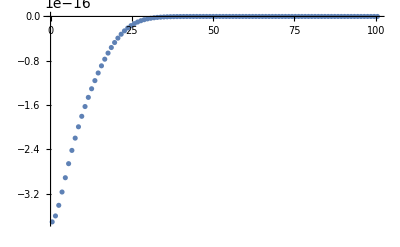

```mathematica
ListPlot[Transpose[List[rlist,deltaUpythonlist]],PlotRange->All]
```

```mathematica
reldeltaUerror = Interpolation[deltaUerror] / Interpolation[deltaUmathlist]
```

InterpolatingFunction[…]/InterpolatingFunction[…]

```mathematica
Plot[reldeltaUerror,{r, rlist[[1]],rlist[[-1]]},AxesLabel->{Style["Abar",Large,Bold],Style["δU",Large,Bold]},PlotStyle->{{Black,Thickness[.005]},{Red,Dashed}},AxesStyle->Black,PlotPoints->1000,PlotRange->All]
```

-Graphics-